Analytical probability to have splitting

```mathematica
Anal[σ_]=Integrate[Cos[x/2]^2 PDF[NormalDistribution[0, σ],x],{x,-∞,∞},Assumptions->σ>0]//FullSimplify
Integrate[Sin[x/2]^2 PDF[NormalDistribution[0, σ],x],{x,-∞,∞},Assumptions->σ>0]//FullSimplify
```

1/2 (1+ⅇ^(-σ^2/2))

1/2-1/2 ⅇ^(-σ^2/2)

Numerical probability to have splitting

```mathematica
Num[σ_]=2/(Erf[π/(√(2 σ^2))] √(2π σ^2))Integrate[Cos[x/2]^2(Exp[-x^2/(2 σ^2)]+Exp[-(x-π)^2/(2 σ^2)]),{x,0,π/2},Assumptions->σ>0]//FullSimplify
```

1/4 (2+(ⅇ^(-σ^2/2) (2 Erf[(π-2 ⅈ σ^2)/(2 √2 σ)]+Erfc[(π-ⅈ σ^2)/(√2 σ)]+Erfc[(π+ⅈ σ^2)/(√2 σ)]-2 Erfc[(π+2 ⅈ σ^2)/(2 √2 σ)]))/Erf[π/(√2 σ)])

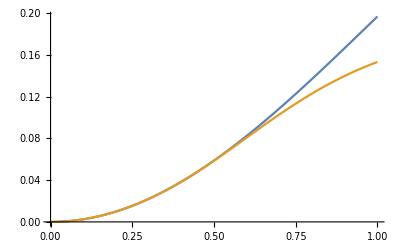

```mathematica
Plot[{1-Anal[x],1-Num[x]},{x,0,1}]//Quiet
```

```mathematica
Pshift[σ_]:=1-Anal[σ]
```

Parameters

```mathematica
shots=20000; (*Number of shots (minus filtered ones)*)
Nch=256;(*Number of states we want (measure of sparsity)*)
Nq=50; (*Number of qubits*)
```

Determining σ

```mathematica
nsp=Ceiling[Log2[Nch]];
eq=1-Sum[PDF[BinomialDistribution[Nq,Pshift[√Σ]],i],{i,0,nsp}]//FullSimplify
sol=NSolve[{eq==1/shots,Σ>0},{Σ}][[1]]
Print["σ = ",√Σ//.sol]
```

1-((1+ⅇ^(-Σ/2))^50)/1125899906842624-(25 (1+ⅇ^(-Σ/2))^49 (1+1/2 (-1-ⅇ^(-Σ/2))))/281474976710656-(1225 (1+ⅇ^(-Σ/2))^48 (1+1/2 (-1-ⅇ^(-Σ/2)))^2)/281474976710656-(1225 (1+ⅇ^(-Σ/2))^47 (1+1/2 (-1-ⅇ^(-Σ/2)))^3)/8796093022208-(57575 (1+ⅇ^(-Σ/2))^46 (1+1/2 (-1-ⅇ^(-Σ/2)))^4)/17592186044416-(264845 (1+ⅇ^(-Σ/2))^45 (1+1/2 (-1-ⅇ^(-Σ/2)))^5)/4398046511104-(3972675 (1+ⅇ^(-Σ/2))^44 (1+1/2 (-1-ⅇ^(-Σ/2)))^6)/4398046511104-(6242775 (1+ⅇ^(-Σ/2))^43 (1+1/2 (-1-ⅇ^(-Σ/2)))^7)/549755813888-(268439325 (1+ⅇ^(-Σ/2))^42 (1+1/2 (-1-ⅇ^(-Σ/2)))^8)/2199023255552

{Σ→0.143766}

σ = 0.379165

```mathematica
σf[shots_,Nch_,Nq_]:=Module[{nsp,eq,sol,Σ},
nsp=Ceiling[Log2[Nch]];
eq=1-Sum[PDF[BinomialDistribution[Nq,Pshift[√Σ]],i],{i,0,nsp}](*//FullSimplify*);
sol=NSolve[{eq==1/shots,Σ>0},{Σ}][[1]];

Return[Σ//.sol]
]
```

Export

```mathematica
out=ParallelTable[{sh,2^nchExp,nq,σf[sh,2^nchExp,nq]},{sh,10^2,10^4,10^2},{nchExp,1,10,1},{nq,15,50,5}];
```

```mathematica
out=Flatten[out,2];
```

```mathematica
(*SetDirectory[StringJoin[NotebookDirectory[],"//Data"]];*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["sigmas.csv",out//N];
```